```mathematica
BMSelect[pop_,T_,b_,d_,sa_,sr_,fit_]:=Module[{noClasses,popsize,U,L,di,ci,mi,li,Ri,Ai,newpop,cbar},
(* This functions calculates changes in abundances according the the variable density lottery model defined in Bertram and Masel 2019 *)
noClasses=Length[pop];
popsize = Total[pop];
U=(T-popsize);
di = Table[d/(1+fit[[i]][[1]]*sa*d),{i,1,noClasses}];
ci=Table[1+fit[[i]][[2]],{i,1,noClasses}];

mi=Table[b pop[[i]]  U/T,{i,1,noClasses}];

li = Table[mi[[i]]/U,{i,1,noClasses}];

cbar = Total[ci*mi]/Total[mi];
L=Total[li];

Ri=Table[
If[NumberQ[(cbar Exp[-li[[i]]](1-Exp[-(L-li[[i]])]))/(ci[[i]]+(cbar L-ci[[i]] li[[i]])/(L-li[[i]])(L-1+Exp[-L])/(1-(1+L)Exp[-L]))],(cbar Exp[-li[[i]]](1-Exp[-(L-li[[i]])]))/(ci[[i]]+(cbar L-ci[[i]] li[[i]])/(L-li[[i]])(L-1+Exp[-L])/(1-(1+L)Exp[-L])),(Exp[-li[[i]]](1-Exp[-(L-li[[i]])]))/(1+(L-1+Exp[-L])/(1-(1+L)Exp[-L]))],{i,1,noClasses}];
Ai=Table[
If[NumberQ[(cbar (1-Exp[-li[[i]]]))/((1-Exp[-li[[i]]])/(1-(1+li[[i]])Exp[-li[[i]]])ci[[i]]li[[i]]+(cbar L-ci[[i]] li[[i]])/(L-li[[i]])(L(1-Exp[-L])/(1-(1+L)Exp[-L])-li[[i]](1-Exp[-li[[i]]])/(1-(1+li[[i]])Exp[-li[[i]]])))],
(cbar (1-Exp[-li[[i]]]))/((1-Exp[-li[[i]]])/(1-(1+li[[i]])Exp[-li[[i]]])ci[[i]]li[[i]]+(cbar L-ci[[i]] li[[i]])/(L-li[[i]])(L(1-Exp[-L])/(1-(1+L)Exp[-L])-li[[i]](1-Exp[-li[[i]]])/(1-(1+li[[i]])Exp[-li[[i]]]))),
(1-Exp[-li[[i]]])/((1-Exp[-li[[i]]])/(1-(1+li[[i]])Exp[-li[[i]]])li[[i]]+(L(1-Exp[-L])/(1-(1+L)Exp[-L])-li[[i]](1-Exp[-li[[i]]])/(1-(1+li[[i]])Exp[-li[[i]]])))]
,{i,1,noClasses}]; 

newpop = Table[If[NumberQ[1/di[[i]](pop[[i]]+U li[[i]](Exp[-L]+(Ri[[i]]+Ai[[i]])ci[[i]]/cbar))],1/di[[i]](pop[[i]]+U li[[i]](Exp[-L]+(Ri[[i]]+Ai[[i]])ci[[i]]/cbar)),0],{i,1,noClasses}];

newpop
];
```

96.

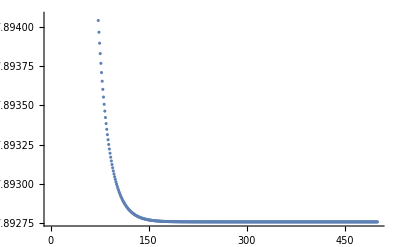

```mathematica
(* Parameters and Examination of quilibrium population sizes with no variation in death rates *)
T=10^9;
b=1;
d=50/48;
sa=0.01;
sr=0.01;
pop={10^8};
fit={{-43,1}};
imax = 1/(sa d)

endTime=500;
nt = Table[{i,pop},{i,1,endTime}];
Quiet[
For[i=2,i≤endTime,i++,
nt[[i]][[2]] =  BMSelect[nt[[i-1]][[2]],T,b,d,sa,sr,fit];
]]
ListPlot[Table[{nt[[i]][[1]],Log10[nt[[i]][[2]][[1]]]},{i,1,Length[nt]}]]
dnt=nt[[2;;endTime]]-nt[[1;;endTime-1]];
```

```mathematica
Neq1=10.0^9 (1-(d(1-sa*fit[[1]][[1]])-1)/(b(1+sa*fit[[1]][[1]]*d)))/nt[[endTime]][[2]][[1]]
Neq2=10.0^9 ((2b)/(b+2))(1-(d(1-sa*fit[[1]][[1]])-1)/(b(1+sa*fit[[1]][[1]]*d)))/nt[[endTime]][[2]][[1]]
Neq3=10.0^9 ((3b+2)/(2(b+2)))(1-(d(1-sa*fit[[1]][[1]])-1)/(b(1+sa*fit[[1]][[1]]*d)))/nt[[endTime]][[2]][[1]];
Neq4=10.0^9 (1-Exp[-b])/(1-Exp[-b]+((d(1-sa*fit[[1]][[1]])-1)/(1+sa*fit[[1]][[1]]*d)))/nt[[endTime]][[2]][[1]]
Mean[{Neq1,((d(1-sa*fit[[1]][[1]])-1)/(b(1+sa*fit[[1]][[1]]*d)))Neq2+(1-(d(1-sa*fit[[1]][[1]])-1)/(b(1+sa*fit[[1]][[1]]*d)))Neq4}]/nt[[endTime]][[2]][[1]]
```

1.44917

0.966112

5.32734

1.86191×10^-8

```mathematica
(d(1-sa*fit[[1]][[1]])-1)/(b(1+sa*fit[[1]][[1]]*d))
```

0.785714

```mathematica
2/1.4
```

1.42857

```mathematica
nt[[endTime-10;;endTime]]
dnt[[endTime-1-10;;endTime-1]]
```

{{490,{7.8119×10^7}},{491,{7.8119×10^7}},{492,{7.8119×10^7}},{493,{7.8119×10^7}},{494,{7.8119×10^7}},{495,{7.8119×10^7}},{496,{7.8119×10^7}},{497,{7.8119×10^7}},{498,{7.8119×10^7}},{499,{7.8119×10^7}},{500,{7.8119×10^7}}}

{{1,{-1.93715×10^-7}},{1,{-1.19209×10^-7}},{1,{-2.23517×10^-7}},{1,{-1.93715×10^-7}},{1,{-1.78814×10^-7}},{1,{-1.04308×10^-7}},{1,{-1.49012×10^-7}},{1,{-1.3411×10^-7}},{1,{-1.63913×10^-7}},{1,{-1.63913×10^-7}},{1,{-7.45058×10^-8}}}

```mathematica
b=12/10;
d=100/98;
s=2/100;
1/(s d)(1-d/(b+1))
```

289/11

```mathematica
49*11-250
```

289

```mathematica
FullSimplify[(Exp[-li](1-Exp[-(L-li)]))/(ci+(cb*L-ci*li)/(L-li) (L-1+Exp[-L])/(1-(1+L)Exp[-L]))ci/1+(1-Exp[-li])/((1-Exp[-li])/(1-(1+li)Exp[-li])ci*li+(cb*L-ci*li)/(L-li)( L(1-Exp[-L])/(1-(1+L)Exp[-L])-li (1-Exp[-li])/(1-(1+li)Exp[-li])))ci/1]
```

ci ⅇ^-li ((1-ⅇ^(-L+li))/(ci+((1+ⅇ^L (-1+L)) (cb L-ci li))/((-1+ⅇ^L-L) (L-li)))+((-1+ⅇ^li) (-1+ⅇ^L-L) (L-li) (1-ⅇ^li+li))/(L (ci li ((-1+ⅇ^li) L+li-ⅇ^L li)+cb ((-1+ⅇ^L) (-1+ⅇ^li) li+L (-1+ⅇ^L (1+li)-ⅇ^li (-1+ⅇ^L+li))))))

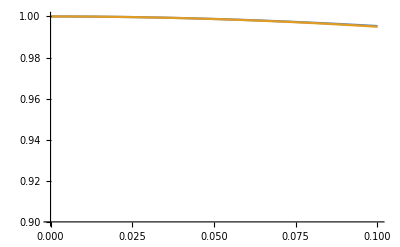

```mathematica
Plot[{(1+x)Exp[-x],1-x^2/2},{x,0,.1},PlotRange->{0.9,1}]
```

```mathematica
γ1[b_,dk_]:=(2b)/(b+2)(1-(dk-1)/b);
iExt[sa_,d_,b_]=Floor[1/(sa d)(1-d/(b+1))];
di[d_,s_,k_]:=d(1+s)^k;
γExt[b_,dk_]:=(1-Exp[-b])/(dk-Exp[-b])+(dk - 1)/(dk - Exp[-b])((Exp[-b]-Exp[-(b(1-Exp[-b]))/(dk-Exp[-b])])/(dk-Exp[-(b(1-Exp[-b]))/(dk-Exp[-b])]));
γOpt[b_,dk_]:=(b+2)/(2b)(1-Sqrt[1-(8(b-dk+1))/(b+2)^2]); 

γTil[b_,dk_,k_,iExt_]:=(k/iExt)γOpt[b,dk] + ((iExt-k)/iExt)γExt[b,dk];
sRel[b_,γ_,s_]:=s((1-γ)(1-(1+b γ)Exp[-b γ]))/(γ+(1-γ)(1-Exp[-b γ]))*(b γ -1+Exp[-b γ])/(b γ (1-Exp[-b γ])+s(1-(1+b γ)Exp[-b γ])) ;
Ua[k_,c_]:=k*c;
βa[sa_,Ua_]:=(Log[sa/Ua])^-2;
βr[sr_,Ur_]:=(Log[sr/Ur])^-2;
αa[γTil_,sa_,Ua_]:=Log[γTil^2×sa×Ua];
αr[γTil_,sr_,Ur_]:=Log[γTil^2×sr×Ur];
Tk[k_,b_,sa_,sr_,d_,Ur_,c_,iExt_]:=Module[{dk,iE,Uab,γT,sre,αab ,βab,αre ,βre},
dk = di[d,sa,-k];
Uab=Ua[-k,c];
γT=γTil[b,dk,-k,iExt];
sre = sRel[b,γT,sr];
αab = αa[γT,sa,Uab];
βab = βa[sa,Uab];
αre = αr[γT,sre,Ur];
βre = βr[sre,Ur];
Return[Exp[-1/2((sa^2 αab βab -sre^2 αre βre)/(sa^2 βab - sre^2 βre))]];
]

Tkexact[k_,b_,sa_,sr_,d_,Ur_,c_,iExt_,γT_]:=Module[{dk,iE,Uab,sre,αab ,βab,αre ,βre},
dk = di[d,sa,-k];
Uab=Ua[-k,c];
sre = sRel[b,γT,sr];
αab = αa[γT,sa,Uab];
βab = βa[sa,Uab];
αre = αr[γT,sre,Ur];
βre = βr[sre,Ur];
Return[Exp[-1/2((sa^2 αab βab -sre^2 αre βre)/(sa^2 βab - sre^2 βre))]];
]
```

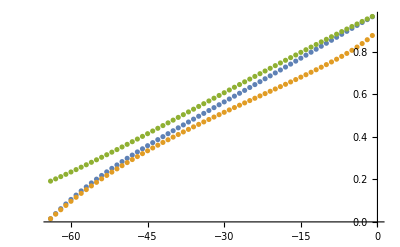

```mathematica
iE = iExt[sa,d,b];
ListPlot[{Table[{k,γTil[b,di[d,sa,-k],-k,iE]},{k,-iE,-1}],Table[{k,γOpt[b,di[d,sa,-k]]},{k,-iE,-1}],Table[{k,γExt[b,di[d,sa,-k]]},{k,-iE,-1}]}]
```

```mathematica
-iE
```

-64

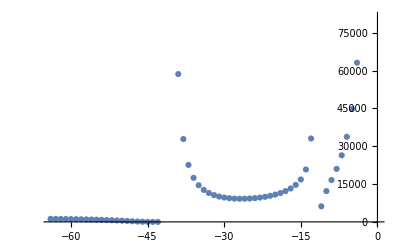

-Graphics-

```mathematica
Ur = 10^-5;
c = 10^-6;
b=2;
d=100/98;
sa=0.01;
sr=.175;
iE = iExt[sa,d,b];
γexact = Table[{k,x/.FindRoot[(1-di[d,sa,-k])*x+(1-x)*(1-Exp[-b*x]),{x,1}][[1]]},{k,-iE,-1}];
ListPlot[{Table[{k,Tkexact[k,b,sa,sr,d,Ur,c,iE,γexact [[-k]][[2]]]},{k,-iE,-1}]}]
ListPlot[{Table[{k,Tk[k,b,sa,sr,d,Ur,c,iE]},{k,-iE,-1}]}]
```

```mathematica
γexact [[1]][[2]]
```

0.014889

```mathematica
Tkexact[-48,b,sa,sr,d,Ur,c,iE,γexact [[38]][[2]]]^2
```

```mathematica
1.6009615071176044*^11/10^10
```

16.0096

```mathematica
NumberForm[1.0793750086774223*^9,9]
```

```mathematica
"1.07937501"×10^("9") / 10^9
```

1.07938

```mathematica
ⅇ^63.65186015446608
```

4.40202×10^27

```mathematica
RealDigits[3.8022002255445704*^7]
```

{{3,8,0,2,2,0,0,2,2,5,5,4,4,5,7,0},8}

```mathematica
NumberForm[3.8022002255445704*^7,16]
```

3.802200225544571×10^7

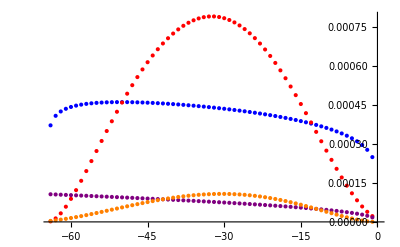

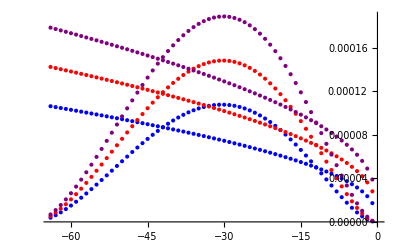

```mathematica
Ts = 10^9;
vr[k_,b_,sa_,sr_,d_,Ur_,c_,iExt_,Ts_]:=Module[{dk,iE,Uab,γT,sre,αab ,βab,αre ,βre},
dk = di[d,sa,-k];
γT=γTil[b,dk,-k,iExt];
sre = sRel[b,γT,sr];
αre = αr[γT,sre,Ur];
βre = βr[sre,Ur];
(* sre^2 βre Log[Ts^2] +sre^2 αre βre *)
Return[sre^2 (Log[Ts^2 γT^2 sre Ur]/Log[sre/Ur])];
]
va[k_,b_,sa_,sr_,d_,Ur_,c_,iExt_,Ts_]:=Module[{dk,iE,Uab,γT,sre,αab ,βab,αre ,βre},
dk = di[d,sa,-k];
Uab=Ua[-k,c];
γT=γTil[b,dk,-k,iExt];
αab = αa[γT,sa,Uab];
βab = βa[sa,Uab];
(* sa^2 βab Log[Ts^2] +sa^2 αab βab *)
Return[sa^2 (Log[Ts^2 γT^2 sa Uab]/Log[sa/Uab])];
]
vrexact[k_,b_,sa_,sr_,d_,Ur_,c_,iExt_,Ts_,γT_]:=Module[{dk,iE,Uab,sre,αab ,βab,αre ,βre},
dk = di[d,sa,-k];
sre = sRel[b,γT,sr];
αre = αr[γT,sre,Ur];
βre = βr[sre,Ur];
(* sre^2 βre Log[Ts^2] +sre^2 αre βre *)
Return[sre^2 ((2Log[Ts γT sre]-Log[ sre /  Ur])/Log[sre/Ur]^2)];
]
vaexact[k_,b_,sa_,sr_,d_,Ur_,c_,iExt_,Ts_,γT_]:=Module[{dk,iE,Uab,sre,αab ,βab,αre ,βre},
dk = di[d,sa,-k];
Uab=Ua[-k,c];
αab = αa[γT,sa,Uab];
βab = βa[sa,Uab];
(* sa^2 βab Log[Ts^2] +sa^2 αab βab *)
Return[sa^2 ((2Log[Ts γT sa]-Log[sa / Uab])/Log[sa/Uab]^2)];
]


Ts1 = 10^9;
Ts2=10^11;
Ts3=10^13;

ListPlot[{Table[{k,va[k,b,sa,sr,d,Ur,c,iE,Ts1]},{k,-iE,-1}],Table[{k,vr[k,b,sa,sr,d,Ur,c,iE,Ts1]},{k,-iE,-1}],Table[{k,vaexact[k,b,sa,sr,d,Ur,c,iE,Ts1,γexact [[-k]][[2]]]},{k,-iE,-1}],Table[{k,vrexact[k,b,sa,sr,d,Ur,c,iE,Ts1,γexact [[-k]][[2]]]},{k,-iE,-1}]},PlotStyle->{Blue,Red,Purple,Orange}]

ListPlot[{Table[{k,vaexact[k,b,sa,sr,d,Ur,c,iE,Ts1,γexact [[-k]][[2]]]},{k,-iE,-1}],Table[{k,vrexact[k,b,sa,sr,d,Ur,c,iE,Ts1,γexact [[-k]][[2]]]},{k,-iE,-1}],Table[{k,vaexact[k,b,sa,sr,d,Ur,c,iE,Ts2,γexact [[-k]][[2]]]},{k,-iE,-1}],Table[{k,vrexact[k,b,sa,sr,d,Ur,c,iE,Ts2,γexact [[-k]][[2]]]},{k,-iE,-1}],Table[{k,vaexact[k,b,sa,sr,d,Ur,c,iE,Ts3,γexact [[-k]][[2]]]},{k,-iE,-1}],Table[{k,vrexact[k,b,sa,sr,d,Ur,c,iE,Ts3,γexact [[-k]][[2]]]},{k,-iE,-1}]},PlotStyle->{Blue,Blue,Red,Red,Purple,Purple}]
```

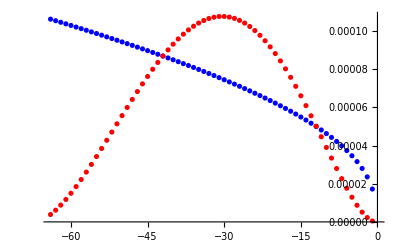

```mathematica
ListPlot[{Table[{k,vaexact[k,b,sa,sr,d,Ur,c,iE,Ts1,γexact [[-k]][[2]]]},{k,-iE,-1}],Table[{k,vrexact[k,b,sa,sr,d,Ur,c,iE,Ts1,γexact [[-k]][[2]]]},{k,-iE,-1}]},PlotStyle->{Blue,Red,Purple,Orange}]
```

```mathematica
ListPlot[{Table[{k,Tkexact[k,b,sa,sr,d,Ur,c,iE,γexact [[-k]][[2]]]},{k,-iE,-1}],Table[{k,Tkexact[k,b,sa,sr,d,Ur,c,iE,γexact [[-k]][[2]]]},{k,-iE,-1}],Table[{k,Tkexact[k,b,sa,sr,d,Ur,c,iE,γexact [[-k]][[2]]]},{k,-iE,-1}]}]
```

```mathematica
sRel[2,.88,0.175]
di[100/98,.01,38]
γexact
```

0.00677523

1.66667

{{-64,0.014889},{-63,0.0368195},{-62,0.0582907},{-61,0.0793278},{-60,0.0999541},{-59,0.120191},{-58,0.140058},{-57,0.159575},{-56,0.178757},{-55,0.197622},{-54,0.216183},{-53,0.234455},{-52,0.25245},{-51,0.270181},{-50,0.287659},{-49,0.304895},{-48,0.321899},{-47,0.33868},{-46,0.355247},{-45,0.371609},{-44,0.387774},{-43,0.403748},{-42,0.41954},{-41,0.435156},{-40,0.450602},{-39,0.465885},{-38,0.48101},{-37,0.495983},{-36,0.510809},{-35,0.525493},{-34,0.54004},{-33,0.554454},{-32,0.56874},{-31,0.582901},{-30,0.596943},{-29,0.610868},{-28,0.62468},{-27,0.638383},{-26,0.651981},{-25,0.665475},{-24,0.67887},{-23,0.692169},{-22,0.705373},{-21,0.718487},{-20,0.731512},{-19,0.744451},{-18,0.757307},{-17,0.770081},{-16,0.782777},{-15,0.795397},{-14,0.807941},{-13,0.820414},{-12,0.832816},{-11,0.845149},{-10,0.857415},{-9,0.869617},{-8,0.881755},{-7,0.893832},{-6,0.905848},{-5,0.917807},{-4,0.929708},{-3,0.941554},{-2,0.953346},{-1,0.965085}}

```mathematica
s = sa
Ns = s Ts1 *γexact [[55]][[2]]
Ub = c*55 *1.0
```

0.01

8.57415×10^6

0.000055

```mathematica
0.01^2((2*Log[8.574153127119546*10^8*.01]-Log[0.01/0.000055])/Log[0.01/0.000055]^2)
```

0.0000987228

```mathematica
Table[{k,sa,Ts1 *γexact [[-k]][[2]],1.0*Ua[-k,c], vaexact[k,b,sa,sr,d,Ur,c,iE,Ts1,γexact [[-k]][[2]]]},{k,-iE,-1}]
```

{{-64,0.01,9.65085×10^8,0.000064,0.000536749},{-63,0.01,9.53346×10^8,0.000063,0.000534287},{-62,0.01,9.41554×10^8,0.000062,0.000531801},{-61,0.01,9.29708×10^8,0.000061,0.00052929},{-60,0.01,9.17807×10^8,0.00006,0.000526753},{-59,0.01,9.05848×10^8,0.000059,0.00052419},{-58,0.01,8.93832×10^8,0.000058,0.000521599},{-57,0.01,8.81755×10^8,0.000057,0.00051898},{-56,0.01,8.69617×10^8,0.000056,0.000516333},{-55,0.01,8.57415×10^8,0.000055,0.000513655},{-54,0.01,8.45149×10^8,0.000054,0.000510947},{-53,0.01,8.32816×10^8,0.000053,0.000508206},{-52,0.01,8.20414×10^8,0.000052,0.000505433},{-51,0.01,8.07941×10^8,0.000051,0.000502625},{-50,0.01,7.95397×10^8,0.00005,0.000499782},{-49,0.01,7.82777×10^8,0.000049,0.000496902},{-48,0.01,7.70081×10^8,0.000048,0.000493985},{-47,0.01,7.57307×10^8,0.000047,0.000491028},{-46,0.01,7.44451×10^8,0.000046,0.000488029},{-45,0.01,7.31512×10^8,0.000045,0.000484989},{-44,0.01,7.18487×10^8,0.000044,0.000481904},{-43,0.01,7.05373×10^8,0.000043,0.000478773},{-42,0.01,6.92169×10^8,0.000042,0.000475594},{-41,0.01,6.7887×10^8,0.000041,0.000472364},{-40,0.01,6.65475×10^8,0.00004,0.000469083},{-39,0.01,6.51981×10^8,0.000039,0.000465747},{-38,0.01,6.38383×10^8,0.000038,0.000462353},{-37,0.01,6.2468×10^8,0.000037,0.0004589},{-36,0.01,6.10868×10^8,0.000036,0.000455384},{-35,0.01,5.96943×10^8,0.000035,0.000451801},{-34,0.01,5.82901×10^8,0.000034,0.00044815},{-33,0.01,5.6874×10^8,0.000033,0.000444425},{-32,0.01,5.54454×10^8,0.000032,0.000440623},{-31,0.01,5.4004×10^8,0.000031,0.000436739},{-30,0.01,5.25493×10^8,0.00003,0.00043277},{-29,0.01,5.10809×10^8,0.000029,0.000428708},{-28,0.01,4.95983×10^8,0.000028,0.00042455},{-27,0.01,4.8101×10^8,0.000027,0.000420288},{-26,0.01,4.65885×10^8,0.000026,0.000415916},{-25,0.01,4.50602×10^8,0.000025,0.000411425},{-24,0.01,4.35156×10^8,0.000024,0.000406808},{-23,0.01,4.1954×10^8,0.000023,0.000402054},{-22,0.01,4.03748×10^8,0.000022,0.000397153},{-21,0.01,3.87774×10^8,0.000021,0.000392092},{-20,0.01,3.71609×10^8,0.00002,0.000386859},{-19,0.01,3.55247×10^8,0.000019,0.000381436},{-18,0.01,3.3868×10^8,0.000018,0.000375806},{-17,0.01,3.21899×10^8,0.000017,0.000369948},{-16,0.01,3.04895×10^8,0.000016,0.000363836},{-15,0.01,2.87659×10^8,0.000015,0.000357442},{-14,0.01,2.70181×10^8,0.000014,0.000350732},{-13,0.01,2.5245×10^8,0.000013,0.000343662},{-12,0.01,2.34455×10^8,0.000012,0.000336183},{-11,0.01,2.16183×10^8,0.000011,0.00032823},{-10,0.01,1.97622×10^8,0.00001,0.000319722},{-9,0.01,1.78757×10^8,9.×10^-6,0.000310556},{-8,0.01,1.59575×10^8,8.×10^-6,0.000300591},{-7,0.01,1.40058×10^8,7.×10^-6,0.000289636},{-6,0.01,1.20191×10^8,6.×10^-6,0.000277415},{-5,0.01,9.99541×10^7,5.×10^-6,0.000263511},{-4,0.01,7.93278×10^7,4.×10^-6,0.000247235},{-3,0.01,5.82907×10^7,3.×10^-6,0.000227323},{-2,0.01,3.68195×10^7,2.×10^-6,0.000200953},{-1,0.01,1.4889×10^7,1.×10^-6,0.000158643}}

```mathematica
Table[{k,vrexact[k,b,sa,sr,d,Ur,c,iE,Ts1,γexact [[-k]][[2]]]},{k,-iE,-1}]
```

{{-64,0.0000207358},{-63,0.0000347053},{-62,0.0000515722},{-61,0.0000710438},{-60,0.0000928486},{-59,0.00011673},{-58,0.000142442},{-57,0.000169749},{-56,0.000198419},{-55,0.000228231},{-54,0.000258964},{-53,0.000290406},{-52,0.000322349},{-51,0.000354589},{-50,0.000386925},{-49,0.000419164},{-48,0.000451114},{-47,0.000482588},{-46,0.000513406},{-45,0.00054339},{-44,0.000572367},{-43,0.000600172},{-42,0.000626642},{-41,0.000651622},{-40,0.000674962},{-39,0.000696517},{-38,0.000716152},{-37,0.000733737},{-36,0.000749148},{-35,0.000762273},{-34,0.000773004},{-33,0.000781247},{-32,0.000786914},{-31,0.000789928},{-30,0.000790225},{-29,0.000787751},{-28,0.000782465},{-27,0.000774339},{-26,0.000763362},{-25,0.000749536},{-24,0.000732881},{-23,0.000713433},{-22,0.00069125},{-21,0.000666408},{-20,0.000639007},{-19,0.00060917},{-18,0.000577046},{-17,0.00054281},{-16,0.000506669},{-15,0.00046886},{-14,0.000429657},{-13,0.00038937},{-12,0.000348348},{-11,0.000306988},{-10,0.000265731},{-9,0.000225072},{-8,0.000185561},{-7,0.000147812},{-6,0.000112504},{-5,0.0000803925},{-4,0.0000523125},{-3,0.000029191},{-2,0.0000120567},{-1,2.0579×10^-6}}

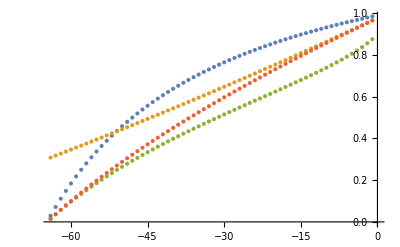

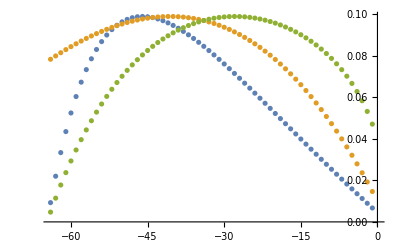

```mathematica
ListPlot[{Table[{k,γ1[b,di[d,sa,-k]]},{k,-iExt,-1}],Table[{k,γ2[b,di[d,sa,-k]]},{k,-iExt,-1}],Table[{k,γ3[b,di[d,sa,-k]]},{k,-iExt,-1}],Table[{k,x/.FindRoot[(1-di[d,sa,-k])*x+(1-x)*(1-Exp[-b*x]),{x,1}][[1]]},{k,-iExt,-1}]}]
ListPlot[{Table[{k,sRel[b,γ1[b,di[d,sa,-k]],sr]},{k,-iExt,-1}],Table[{k,sRel[b,γ2[b,di[d,sa,-k]],sr]},{k,-iExt,-1}],Table[{k,sRel[b,γ3[b,di[d,sa,-k]],sr]},{k,-iExt,-1}],Table[{k,sRel[b,γ3[b,di[d,sa,-k]],sr]},{k,-iExt,-1}]}]
```

```mathematica
Table[sRel[b,γ1[b,di[d,sa,-k]],sr],{k,-iExt,-1}]
Table[sRel[b,γ2[b,di[d,sa,-k]],sr],{k,-iExt,-1}]
```

{0.0092773,0.0219923,0.0333576,0.0434737,0.0524373,0.0603403,0.0672694,0.073306,0.078526,0.0829997,0.0867924,0.0899642,0.0925704,0.0946619,0.0962854,0.0974834,0.0982953,0.0987567,0.0989004,0.0987563,0.0983516,0.0977112,0.096858,0.0958126,0.094594,0.0932195,0.0917049,0.0900646,0.0883117,0.0864583,0.0845152,0.0824925,0.0803993,0.0782439,0.076034,0.0737765,0.0714776,0.0691433,0.0667788,0.0643889,0.061978,0.0595501,0.0571088,0.0546576,0.0521994,0.049737,0.0472728,0.0448093,0.0423485,0.0398922,0.0374423,0.0350001,0.0325672,0.0301448,0.0277341,0.025336,0.0229516,0.0205815,0.0182267,0.0158877,0.0135652,0.0112596,0.00897144,0.00670106}

{0.0782937,0.079896,0.0814438,0.0829358,0.0843706,0.0857469,0.0870632,0.0883183,0.0895106,0.0906389,0.0917017,0.0926975,0.093625,0.0944826,0.095269,0.0959826,0.096622,0.0971856,0.0976721,0.0980798,0.0984074,0.0986532,0.0988157,0.0988935,0.0988849,0.0987884,0.0986026,0.0983257,0.0979563,0.0974929,0.0969338,0.0962775,0.0955224,0.0946669,0.0937095,0.0926486,0.0914827,0.0902101,0.0888293,0.0873387,0.0857367,0.0840219,0.0821925,0.0802472,0.0781842,0.0760021,0.0736994,0.0712744,0.0687257,0.0660517,0.0632509,0.0603218,0.057263,0.0540729,0.05075,0.0472929,0.0437002,0.0399703,0.0361019,0.0320935,0.0279438,0.0236513,0.0192147,0.0146326}

```mathematica
x/.FindRoot[(1-di[d,sa,30])*x+(1-x)*(1-Exp[-b*x]),{x,1}][[1]]
```

0.596943